```mathematica
(* Routine to produce solution *)
FindSol:=(i=0;interstep={};
{minim,minsolrep}=Monitor[FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;norm=normedrel.normedrel//N;If[i>MyMaxIterations,Throw["Too big step"]];AppendTo[interstep,nvars])],Row@{"Step: " ,i,",   Minim: ",norm}];AppendTo[NoSteps,i];AppendTo[Steps,interstep]);
SilentFindSol:=(i=0;
interstep={};{minim,minsolrep}=FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw["Too big step"]];AppendTo[interstep,nvars])];AppendTo[NoSteps,i];AppendTo[Steps,interstep]);
```

```mathematica
(* Iteration procedure *)
Iteratemyver[syt_]:=Block[{},
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,If[step<10^-20,Print[{syt,step//N,Λvals//N}];Break[],
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqns[Λnew];
Which[
Catch[SilentFindSol]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]];
]],
Row@{"Current Λ history is: ",Λvals//N,"current Λ is: ",ΛLast//N, "   step is: ",step//N}];
];
```

```mathematica
MyMaxIterations=12;base=2;pmin=3;RecoverySpeed=1/3;prec=80;interpord=40;

SolutionFromSYTmyver[SYT_]:=Block[{},
NoSteps={};
Steps={};
λT=SYT;
λ=SYT//ToYD;
GenerateQsystem[λ];
LargeΛExpansion;
SubleadingOrders;
GenerateEqnsForNumerics;
SolveAtΛ0;
GenerateSolsFromAsymptotics;
Λvals=Λvals0;
(* the previous line resets Λvals - a record for which Λ solution was already found *)
Iteratemyver[SYT];
Steps=Steps[[2;;]];
Steps={Λvals[[#]],vars2nvars/.Λ->Λvals[[#]]/.(Thread[nvars->#]&)/@Steps[[#]]}&/@Range[Length[Steps]];
{Λvals,vars2nvars/.Λ->Λvals[[#]]/.sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0]/.vars2nvars/.Λ->Λvals[[#]]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}
];
```

```mathematica
yd={4,2,1};
L=Total[yd];
rigs=ModestoRiggedConfig[L,#]&/@ModesConfig[yd];
syts=ToSYT/@rigs;
```

```mathematica
NoStepsAll={};
StepsAll={};
lazyans=Module[{ans},ans=SolutionFromSYTmyver[#];AppendTo[NoStepsAll,NoSteps];AppendTo[StepsAll,Steps];ans]&/@syts;
(*Monitor[(AppendTo[lazyans,SolutionFromSYTmyver[#]];syt=#)&/@syts,syt];*)
```

35

30

{{8,28,31},{16,18},{19,23},{20,26}}

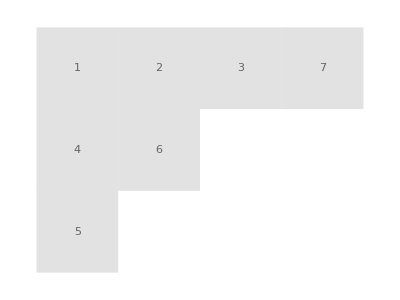
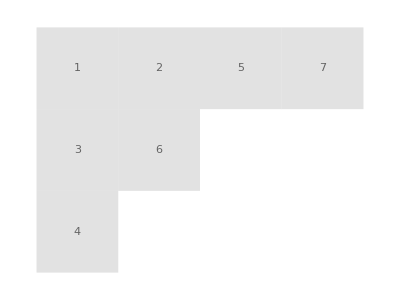
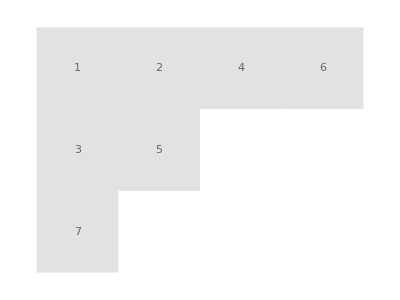
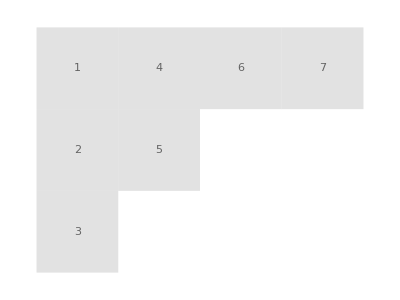
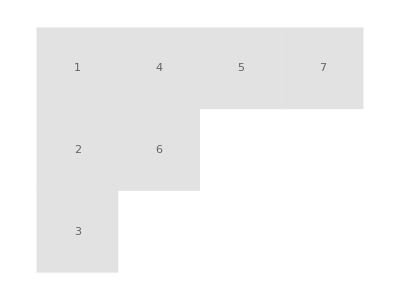
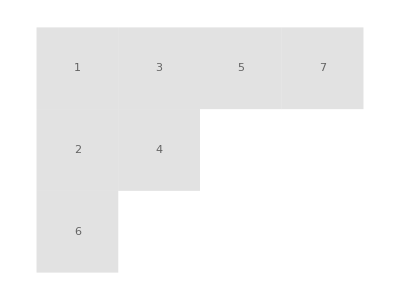
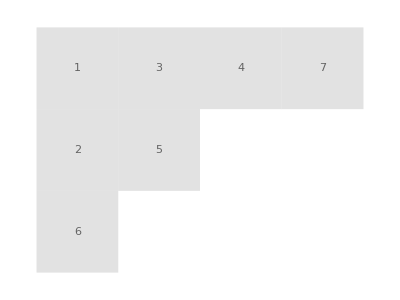
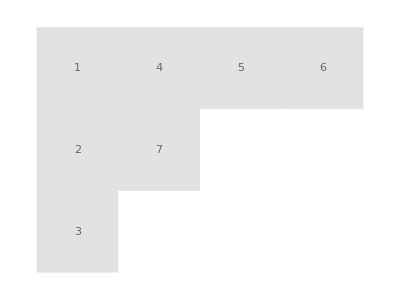

```mathematica
a=1;
Round[lazyans[[All,3,-1]],10^-3]//N//Length
Round[lazyans[[All,3,-1]],10^-3]//N//DeleteDuplicates//Length

repeats=If[#[[2]]>1,{#[[1]]//Flatten,Position[Round[lazyans[[All,3,-1,a]],10^-3]//N,#[[1]]]//Flatten},Nothing]&/@Tally[Round[lazyans[[All,3,-1,a]],10^-3]//N];
repeatlist=repeats[[All,2]]

showSYT/@ToSYT/@rigs[[#]]&/@repeatlist
```

```mathematica
lazyansone=SolutionFromSYTmyver[syts[[20]]];
```

```mathematica
NoSteps;

lazyansone[[1]]//N;
%//ListPlot;

deltalambda=Table[lazyansone[[1,i]]-lazyansone[[1,i+1]],{i,Length[lazyansone[[1]]]-1}]//ListPlot;

Table[Table[pdist[Steps[[no]][[i]],Steps[[no]][[i+1]],2],{i,Length[Steps[[no]]]-1}],{no,Length[Steps]}];
%//ListLinePlot[#,PlotRange->All,PlotLegends->lazyansone[[1]]]&;
```

```mathematica
(*Distance function, L^p*)
pdist[vec1_,vec2_,p_,uast_:1]:=Total[Abs[vec1-vec2]^p*uast]^(1/p)
```

```mathematica
(*Finding distances between solutions (for different rigged configurations, numbered by no1, no2) for chosen lists of Lambda values; lambdalist is a descending list*)
coeffStraightlines[positions_,lambdalist_,lambda_]:=Module[{baselambda,baseposition,foundpositions},baselambda=SelectFirst[lambdalist//Reverse,#>=lambda&];
baseposition=Position[lambdalist,baselambda][[1,1]];
foundpositions=If[lambda!=lambdalist[[-1]],positions[[baseposition]]+(positions[[baseposition+1]]-positions[[baseposition]])/(lambdalist[[baseposition+1]]-baselambda)*(lambda-baselambda),positions[[-1]]]]

distanceChooseLambda[ans_,no1_,no2_,lambdalist_]:=pdist[coeffStraightlines[ans[[no1,2,All,All,2]],ans[[no1,1]],#],coeffStraightlines[ans[[no2,2,All,All,2]],ans[[no2,1]],#],2]&/@lambdalist
```

```mathematica
repeatlistsets=Subsets[#,{2}]&/@repeatlist;
Distanceslistssets=Map[(Lambdalistshared=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater];distanceChooseLambda[lazyans,#[[1]],#[[2]],Lambdalistshared])&,repeatlistsets,{2}];
dist=Map[Part[#,-6;;-1]&,Distanceslistssets,{2}]//Round
```

{{{4849,984,177,33,4,0},{564,131,13,0,0,0},{6974,1537,306,45,4,0}},{{6,3,2,0,0,0}},{{38,9,4,2,1,0}},{{2170,330,48,5,0,0}}}

```mathematica
Lambdalist=lazyans[[4,1]];
distanceChooseLambda[lazyans,4,7,Lambdalist]//Round;
```

```mathematica
no=30;
deltalambda=Table[lazyans[[no,1,i]]-lazyans[[no,1,i+1]],{i,Length[lazyans[[no,1]]]-1}];
Table[pdist[lazyans[[no,2,i,All,2]],lazyans[[no,2,i+1,All,2]],2],{i,Length[lazyans[[no,2]]]-1}]//Round;
```

```mathematica
PlotQmyver[avalues_,color_:{Blue,PointSize[0.01]}]:=Map[Replace[x_:>{Re[x],Im[x]}],avalues,{2}]//ListPlot[#,PlotStyle->color,ImageSize->Medium]&;

ColorCodes1=Darker/@{Blue,Green,Yellow,Pink,Cyan,Magenta,Red,Orange,Gray,Black};
ColorCodes2=Lighter/@{Blue,Green,Yellow,Pink,Cyan,Magenta,Red,Orange,Gray,Black};

ManipulatePlotmyver[values1_,values2_,Λvals1_,Λvals2_]:=Manipulate[
Row[{Row[{"Λs=",{SetAccuracy[Λvals1[[k]],3],SetAccuracy[Λvals2[[kk]],3]}}],Show[{PlotQmyver@@@Reverse[Table[{{values1[[k]][[a]],values2[[kk]][[a]]},{{ColorCodes1[[a]],PointSize@Sizes[[a]]},{ColorCodes2[[a]],PointSize@Sizes[[a]]}}},{a,Length[λ]-1}]]}]}],{{k,1,Row[Prepend[Table[ColorCodes1[[i]],{i,Length[λ]-1}],"no1 "]]},1,Length[Λvals1],1},{{kk,1,Row[Prepend[Table[ColorCodes2[[i]],{i,Length[λ]-1}],"no2 "]]},1,Length[Λvals2],1}];
```

```mathematica
no1=4;
no2=7;
ManipulatePlotmyver[-lazyans[[no1,3]]+1,-lazyans[[no2,3]]+1,lazyans[[no1,1]],lazyans[[no2,1]]]
```

```mathematica
size[vec_]:=Total[Abs[vec]^2]^(1/2)
sizes=GroupBy[Flatten[Transpose/@Map[{#[[1]],size/@(#[[2]]//Values)}&,lazyans],1],First][[All,All,2]];
```

```mathematica
comp=1;
lists=Table[If[i!=comp,{comp,i},Nothing],{i,Length[lazyans[[All,3,-1]]]}];
lists={{4,7}};
lists=Subsets[Range[1,Length[lazyans]],{2}];
showSYT/@ToSYT/@rigs[[#]]&/@lists;

normdistancesprev=Module[{Ltest},{(Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater])[[2;;]],
Table[pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
/Max[sizes[Ltest [[Position[Ltest,i][[1,1]]-1]]]]
,{i,Ltest[[2;;]]}]}//Transpose]&/@lists;
normdistances=Module[{Ltest},{Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater],
Table[pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
/Max[sizes[i]]
,{i,Ltest}]}//Transpose]&/@lists;
distances=Module[{Ltest},{Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater],
Table[
pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
,{i,Ltest}]
}//Transpose]&/@lists;
```

```mathematica
test=GroupBy[Flatten[normdistances,1],First][[All,All,2]];
Table[{i,Min[test[i]]},{i,test//Keys}]//ListPlot;
```

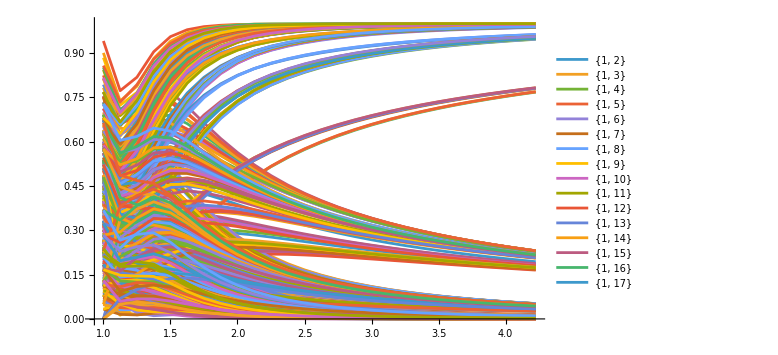

```mathematica
(*plotdist=#[[1;;-1]]&/@normdistances;*)
normdistances//ListLinePlot[#,PlotLegends->ToString/@lists,ImageSize->Large,PlotRange->All]&
```

```mathematica
comp=16;
val=Range[1,Length[lazyans]];
val={comp,18};
```

```mathematica
(*soltest={lazyans[[comp,1]],StepsAll[[comp]][[All,-1]]}//Transpose;*)
coeffinterp[comp_]:=AssociationThread[StepsAll[[comp,All,1]],StepsAll[[comp,All,2,1]]];

lazyanscoeff[v_]:=AssociationThread[lazyans[[v,1]],lazyans[[v,2]]];
Lambdashared[comp_,v_]:=Sort[Intersection[lazyans[[comp,1]],lazyans[[v,1]]],Greater];
```

```mathematica
disttocomppolinterp=Table[{i,pdist[coeffinterp[comp][i]//Values,lazyanscoeff[v][i]//Values,2]},{v,val},{i,Lambdashared[comp,v]}];
normdisttocomppolinterp=Table[{i,pdist[coeffinterp[comp][i]//Values,lazyanscoeff[v][i]//Values,2]/Max[sizes[i]]},{v,val},{i,Lambdashared[comp,v]}];
```

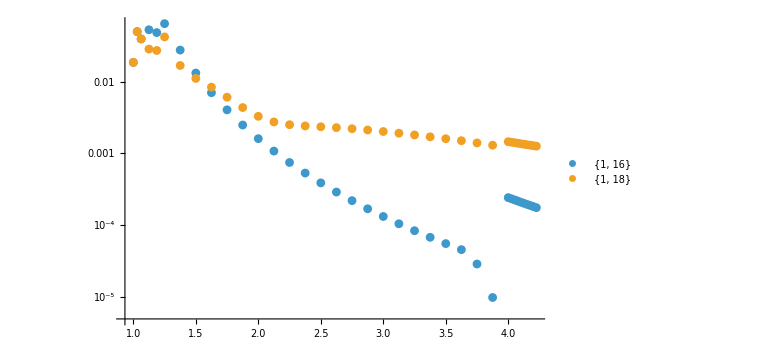

```mathematica
plotdist=#[[1;;-1]]&/@normdisttocomppolinterp;
plotdist//ListLogPlot[#,PlotLegends->ToString/@Table[{comp,i},{i,val}],ImageSize->Large,PlotRange->All]&
```

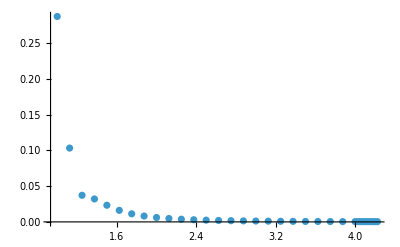

```mathematica
Table[{i,pdist[coeffinterp[28][i]//Values,coeffinterp[30][i]//Values,2]/Max[sizes[i]]},{i,Lambdashared[28,30]}]//ListPlot[#,PlotRange->All]&
```

```mathematica
Manipulate[{(Replace[x_:>{-Re[x]+1,Im[x]}])/@(u/.Table[NSolve[YQa[a,0]/.StepsAll[[1,i,2,1]]],{a,Length[λ]-1}][[1]]),(Replace[x_:>{-Re[x]+1,Im[x]}])/@(u/.Table[NSolve[YQa[a,0]/.StepsAll[[22,j,2,1]]],{a,Length[λ]-1}][[1]]),(Replace[x_:>{-Re[x]+1,Im[x]}])/@(lazyans[[1,3,k,1]]),(Replace[x_:>{-Re[x]+1,Im[x]}])/@(lazyans[[22,3,l,1]])}//ListPlot[#,PlotRange->All,PlotStyle->{Green,Blue,Red,Yellow,Black}]&,{i,1,Length[StepsAll[[1]]],1},{j,1,Length[StepsAll[[22]]],1},{k,1,Length[lazyans[[1,3]]],1},{l,1,Length[lazyans[[22,3]]],1}]
```